```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/lackey/Research/Poisson/Testprograms

## Chebyshev polynomials

```mathematica
(*f[x_]:=Sum[ChebyshevT[2*n+1, x], {n, 0, 3}]
Expand[f[x]]*)
f[x_]:=Cos[x]
```

```mathematica
f'[x]
```

-Sin[x]

```mathematica
g[n_]:=Integrate[2/(π*(1+KroneckerDelta[0, n]))(f[x]*ChebyshevT[n, x])/(√(1-x^2)), {x, -1, 1}]
```

```mathematica
gprime[n_]:=Integrate[2/(π*(1+KroneckerDelta[0, n]))(f'[x]*ChebyshevT[n, x])/(√(1-x^2)), {x, -1, 1}]
```

```mathematica
gcoeff=N[Table[g[n], {n, 0, 10}]]
```

{0.765198,0.,-0.229807,0.,0.00495328,0.,-0.0000418767,0.,1.88418×10^-7,0.,0.}

```mathematica
gprimecoeff=N[Table[gprime[n], {n, 0, 10}]]
```

{0.,-0.880101,0.,0.0391267,0.,-0.000499515,0.,3.00465×10^-6,0.,-1.02445×10^-8,0.}

```mathematica
chebtable=Table[ChebyshevT[n, x], {n, 0,10}]
```

{1,x,-1+2 x^2,-3 x+4 x^3,1-8 x^2+8 x^4,5 x-20 x^3+16 x^5,-1+18 x^2-48 x^4+32 x^6,-7 x+56 x^3-112 x^5+64 x^7,1-32 x^2+160 x^4-256 x^6+128 x^8,9 x-120 x^3+432 x^5-576 x^7+256 x^9,-1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10}

```mathematica
gprimecoeff.chebtable
```

0.-0.880101 x+0. (-1+2 x^2)+0.0391267 (-3 x+4 x^3)+0. (1-8 x^2+8 x^4)-0.000499515 (5 x-20 x^3+16 x^5)+0. (-1+18 x^2-48 x^4+32 x^6)+3.00465×10^-6 (-7 x+56 x^3-112 x^5+64 x^7)+0. (1-32 x^2+160 x^4-256 x^6+128 x^8)-1.02445×10^-8 (9 x-120 x^3+432 x^5-576 x^7+256 x^9)+0. (-1+50 x^2-400 x^4+1120 x^6-1280 x^8+512 x^10)

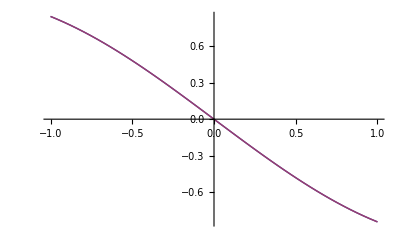

```mathematica
Plot[{-Sin[x], gprimecoeff.chebtable}, {x, -1, 1}]
```

## 1/sin acting on sin series

```mathematica
f[x_]:=Sum[Sin[n*x], {n, 1, 5}]/Sin[x]
```

```mathematica
f[3.4]
```

2.20527

```mathematica
g[n_]:=Integrate[1/(π(1+KroneckerDelta[0, n]))f[x]*Cos[n*x], {x, 0, 2π}]
```

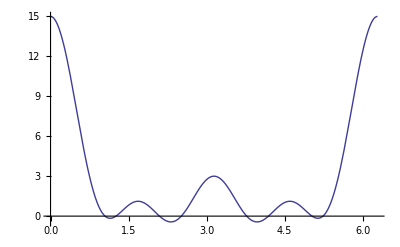

```mathematica
Plot[f[x], {x, 0, 2π}]
```

```mathematica
gcoeff=N[Table[g[n], {n, 0, 10}]]
```

{3.,4.,4.,2.,2.,0.,0.,0.,0.,0.,0.}

```mathematica
costable=Table[Cos[n*x], {n, 0,10}]
```

{1,Cos[x],Cos[2 x],Cos[3 x],Cos[4 x],Cos[5 x],Cos[6 x],Cos[7 x],Cos[8 x],Cos[9 x],Cos[10 x]}

```mathematica
gcoeff.costable
```

3.+4. Cos[x]+4. Cos[2 x]+2. Cos[3 x]+2. Cos[4 x]+0. Cos[5 x]+0. Cos[6 x]+0. Cos[7 x]+0. Cos[8 x]+0. Cos[9 x]+0. Cos[10 x]

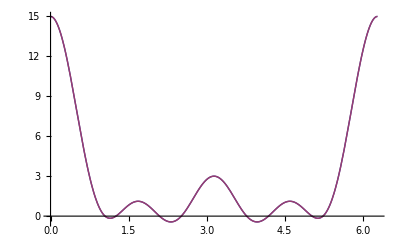

```mathematica
Plot[{f[x], gcoeff.costable}, {x, 0, 2π}]
```

## 1/sin acting on appropriate cos series (made from associated Legendre functions)

105/256 (10+288 Cos[x]+17 Cos[2 x]-432 Cos[3 x]+6 Cos[4 x]+144 Cos[5 x]-33 Cos[6 x])

4.10156+118.125 Cos[x]+6.97266 Cos[2 x]-177.188 Cos[3 x]+2.46094 Cos[4 x]+59.0625 Cos[5 x]-13.5352 Cos[6 x]

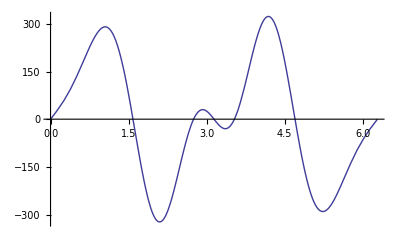

```mathematica
TrigReduce[Expand[LegendreP[6, 2, Cos[x]]+LegendreP[5, 4, Cos[x]]]]
TrigReduce[N[Expand[LegendreP[6, 2, Cos[x]]+LegendreP[5, 4, Cos[x]]]]]
f[x_]:=(LegendreP[6, 2, Cos[x]]+LegendreP[5, 4, Cos[x]])/Sin[x]
Plot[f[x], {x, 0, 2π}]
```

```mathematica
g[n_]:=Integrate[1/π f[x]*Sin[n*x], {x, 0, 2π}]
```

{0,8.203125,236.25,22.1484375,-118.125,27.0703125,0,0,0,0,0}

{0,Sin[x],Sin[2 x],Sin[3 x],Sin[4 x],Sin[5 x],Sin[6 x],Sin[7 x],Sin[8 x],Sin[9 x],Sin[10 x]}

8.203125 Sin[x]+236.25 Sin[2 x]+22.1484375 Sin[3 x]-118.125 Sin[4 x]+27.0703125 Sin[5 x]

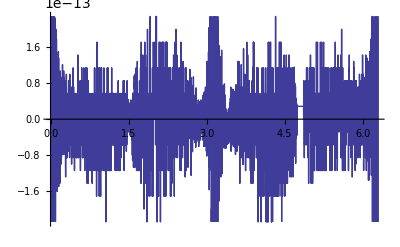

```mathematica
gcoeff=N[Table[g[n], {n, 0, 10}], 20]
sintable=Table[Sin[n*x], {n, 0,10}]
gcoeff.sintable
Plot[{f[x]-gcoeff.sintable}, {x, 0, 2π}]
```

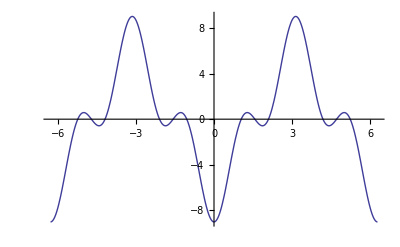

```mathematica
j=3;
Plot[Cos[θ]/Sin[θ](-j Sin[j θ]), {θ, -2π, 2π}, PlotRange->All]
```

```mathematica
Plot[-3Cos[3 θ]-6Cos[θ], {θ, -2π, 2π}, PlotRange->All]
```

-Graphics-